```mathematica
Manipulate[ContourPlot[q1/Norm[{x,y}-p[[1]]]+q2/Norm[{x,y}-p[[2]]],{x,-2,2},{y,-2,2},Contours->20,PlotRangePadding->0,Frame->False,PlotPoints->40,ImageSize->Scaled[1],ColorFunction->"DarkRainbow"],{{q1,-1},-3,3},{{q2,2},-3,3},{{p,{{-1,0},{1,0}}},{-1,-1},{1,1},Locator},Deployed->True,FrameMargins->0,ContentSize-> {500,500}]
```

```mathematica
Animate[Plot[Sin[a+x],{x,0,10}],{a,0,10}]
```

```mathematica
f[t_]:=-t^3+4 t^2-t-4
Plot[f[t],{t,-1,5}]
```

```mathematica
F[s_]:=-6/s^4+8/s^3-1/s^2-4/s
```

```mathematica
fapp[t_,c_,r_]:=NIntegrate[F[c+I u] E^((c+I u) t),{u,-r,r}]/ (2 Pi)
```

```mathematica
Animate[Plot[fapp[t,1,r],{t,-1,4}],{r,1,5}]
```

```mathematica
Plot[{fapp[t,1,10],f[t]},{t,-1,4},PlotLabels->"Expressions"]
```

```mathematica
Plot[Re[F[1+I c]],{c,-10,10}]
```

```mathematica
s[x_]:=1/2+NIntegrate[Sin[t]/t,{t,0,x}]/Pi
```

```mathematica
Plot[s[x],{x,-1000,1000}]
```

```mathematica
ss[x_]:=Sin[x]/x
aa=Animate[Plot[ss[x],{x,0,r}],{r,0,100}];
```

```mathematica
Export["aa.mp4",aa]
```

```mathematica
NIntegrate[ss[x],{x,0,Infinity}]
```

```mathematica
N[Pi/2]
```

```mathematica
Clear[f,F,f1]
c=2;
inf=2;
inf2=Pi;
f[t_]:=N[Sin[t]]
F[s_?NumericQ,trg_]:=NIntegrate[f[t] E^(-s t),{t,0,trg}]
f1[u_,trg_,frg_,c_]:=1/Pi  NIntegrate[Re[F[c+I im,trg] E ^ ((c+I im)u)],{im,0,frg}]
```

```mathematica
ListPlot[Table[{x,f1[x,inf,inf2,c]},{x,0,Pi,Pi/4}],Joined->True,InterpolationOrder->2]
```

```mathematica
inf2=2;
inf=0.1;
c=2;
splot0=ListPlot[Table[{x,f1[x,inf,inf2,c]},{x,0,Pi,Pi/16}],Joined->True,InterpolationOrder->2,PlotStyle->Red];
inf=1;
splot1=ListPlot[Table[{x,f1[x,inf,inf2,c]},{x,0,Pi,Pi/16}],Joined->True,InterpolationOrder->2,PlotStyle->Red];
inf=2;
splot2=ListPlot[Table[{x,f1[x,inf,inf2,c]},{x,0,Pi,Pi/16}],Joined->True,InterpolationOrder->2,PlotStyle->Red];
inf=3;
splot3=ListPlot[Table[{x,f1[x,inf,inf2,c]},{x,0,Pi,Pi/16}],Joined->True,InterpolationOrder->2,PlotStyle->Red];
inf=4;
splot4=ListPlot[Table[{x,f1[x,inf,inf2,c]},{x,0,Pi,Pi/16}],Joined->True,InterpolationOrder->2,PlotStyle->Red];
inf=5;
splot5=ListPlot[Table[{x,f1[x,inf,inf2,c]},{x,0,Pi,Pi/16}],Joined->True,InterpolationOrder->2,PlotStyle->Red];
tplot=ListPlot[Table[{x,f[x]},{x,0,Pi,Pi/16}],Joined->True,InterpolationOrder->2,PlotStyle->Blue];
Show[splot1,splot2,tplot,splot0,splot3,splot4]
Show[splot0]
Show[splot1]
Show[splot2]
Show[splot3]
Show[splot4]
Show[splot5]
Show[tplot]
```

```mathematica
g[s_?NumericQ]:=LaplaceTransform[f[t],t,s]
```

```mathematica
g1[t_]:=InverseLaplaceTransform[g[s],s,t]
```

```mathematica
Plot[g1[t],{t,0,Pi}]
```

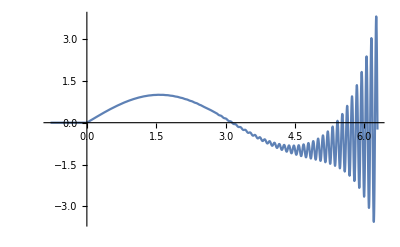

```mathematica
Clear[g,f2]
g[s_?NumericQ]:=LaplaceTransform[f[t],t,s]
f2[u_,frg_,c_]:=1/Pi  NIntegrate[Re[1/(1+(c+I im)^2) E ^ ((c+I im)u)],{im,0,frg}]
c=2;
frg=60;
Plot[f2[t,frg,c],{t,-Pi/4,2Pi}]
```

```mathematica
f2[1,1,2]
```

```mathematica
LaplaceTransform[Sin[t],t,s]
```

1/(1+s^2)

```mathematica
(* Simple integral approximation by riemann sums *)
(*                                               *)    
(* INPUT:  fn function of x to approximate double integral *)
(*         (a,b) range of X variable (ax<bx) (rangex) *)
(*         n defines the approximation of dx as range/2^n DEFAULT: n=9 *)
(*         v verbose (True or False) DEFAULT: v=False *)
(* OUTPUT: Simple integral approximation by riemann sums *)

SimpleRiemannSum[fn_,a_,b_,n_:9,v_:False]:=
(SeedRandom[];
range=b-a;
dx=N[range/2^n];
If[v,Print["range=",range]];
If[v,Print["n=",n]];
If[v,Print["dx=",dx]];
Somma=0;
For[k=0;x=a,k<2^n,k++,
Somma+=fn[x+dx RandomReal[]];
If[v,Print["x=",k,"\tSomma=",Somma dx]];
x+=dx
];
Somma*=dx;
If[v,Print["Somma=",Somma]];
Return[N[Somma]])
```

```mathematica
Clear[f]
f[x_]:=Cos[x]/(x^2+1)
l=1000;
SimpleRiemannSum[f,-l,l,16]
N[Pi/E]
```

1.15135

1.15573

```mathematica
Clear[f,F,f1]
a=3;
c=-4;
inf=10;
inf2=10;
f[t_]:=N[E^(-a t)]
F[s_?NumericQ,trg_]:=NIntegrate[f[t] E^(-s t),{t,0,trg}]
f1[u_,trg_,frg_,c_]:=1/Pi  NIntegrate[Re[F[c+I im,trg] E ^ ((c+I im)u)],{im,0,frg}]
f1[2,inf,inf2,c]
f[2]
```

0.00315987

0.00247875

```mathematica
F[-4,100]
```

2.68812×10^43

```mathematica
Clear[f]
f[x_]:=(Sin[x])^2/(x^2 (x^2+1))
l=1000;
SimpleRiemannSum[f,0,l,16]
N[Pi/4(1+E^-2)]
```

0.892057

0.89169